```mathematica
p=Normal@Series[ComplexExpand[1/Abs@(Subscript[b, 0]+Subscript[b, 1] ϕ+Subscript[b, 2] ϕ^2), {Subscript[b, 0], Subscript[b, 1], Subscript[b, 2]}], {ϕ, 0, 2}]/.{ϕ->√(Γ/Re[Subscript[b, 1]])x};
noExp = Normal@Series[Exp[(-Re[Subscript[b, 2]/6] ϕ^3-Re[Subscript[b, 3]/24] ϕ^4)/Γ]/.{ϕ->√(Γ/Re[Subscript[b, 1]])x}, {Γ, 0, 1}];
newpol = CoefficientList[Normal@Series[noExp * p,  {Γ, 0, 1}], x];
intmonom = Table[Assuming[kk>0,Integrate[Exp[-x^2 - I kk x] x^(n-1), {x, -Infinity, Infinity}]], {n, 7}];
res=Normal@Series[Total[(newpol*intmonom)/(ⅇ^(-kk^2/4))/.{kk->k*√(Γ/Re[Subscript[b, 1]])}], {Γ, 0, 1}];
b2=I^2/(1-I Rs)^3(w-2 w^2)/.{w->-I Rs};
b3=I^3/(1-I Rs)^5(-5 w(w-2 w^2)+(w+w^2)(w-2 w^2))/.{w->-I Rs};
rules={Subscript[b, 0]->1-I Rs, Subscript[b, 1]->Rs/(1-I Rs), Subscript[b, 2]->b2, Subscript[b, 3]-> b3};
ress=res/.rules//ComplexExpand;
akaAk = Total[(CoefficientList[Normal@Series[ress//Simplify, {Γ, 0, 1}], Γ]//Simplify)*{1, Γ}];
{A0, A1}=CoefficientList[akaAk, k]/{1, 2I Γ}
```

{(√π)/(√(1+Rs^2))+(√π Rs (503-1142 Rs^2-49 Rs^4+12 Rs^6) Γ)/(192 (1+Rs^2)^(7/2)),(√π (-1+3 Rs^2))/(16 (1+Rs^2)^(3/2))}

{(√π)/(√(1+Rs^2))+(503 √π Rs Γ)/(192 (1+Rs^2)^(7/2))-(571 √π Rs^3 Γ)/(96 (1+Rs^2)^(7/2))-(49 √π Rs^5 Γ)/(192 (1+Rs^2)^(7/2))+(√π Rs^7 Γ)/(16 (1+Rs^2)^(7/2)),(ⅈ √π (-1+3 Rs^2) Γ)/(8 (1+Rs^2)^(3/2)),-(√π √(1+Rs^2) Γ)/(4 Rs)}

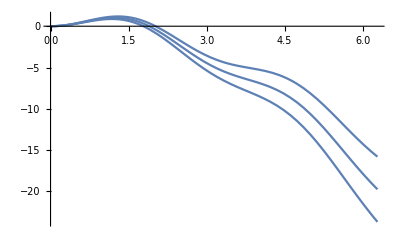

```mathematica
Plot[Table[1-Cos[2x] - χ x^2, {χ, 0.4, 0.6, 0.1}], {x, 0, 2π}]
```

```mathematica
Sum[x^(2n)/(n!(n+k)!), {n, 0, Infinity}]
```

x^-k BesselI[k,2 x]